```mathematica
vars  ={Ntot-> 225, Con-> 8, k->15, fN->2.3021, gN-> 0.1465};
h[p_,i_]:= - (Con-1)/2 (1+4 fN p (1-p) i + (2p-1)^2 fN) - (2p-1)((Con+1)/2(1+fN) - k);
Plot3D[h[p,i]/. vars, {p,0,1}, {i,-1,1}];
```

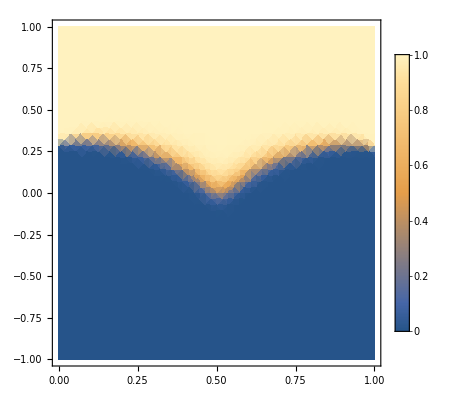

```mathematica
μON[p_,i_] := fN ( Con p + (1-p) + (Con-1)(1-p)i);
μOFF[p_,i_] := fN ( Con p + (1-p) - (Con-1)p i);
σ[p_,i_]:= (Con-1) Sqrt[gN p (1-p)];
Ponon[p_,i_] := 1 -CDF[NormalDistribution[μON[p,i], σ[p,i]], k-Con];
Poffoff[p_,i_]:=CDF[NormalDistribution[μOFF[p,i], σ[p,i]], k-1];
Peq[p_,i_]:= Ponon[p,i]^(p*Ntot) Poffoff[p,i]^((1-p)*Ntot);
DensityPlot[Peq[p,i]/.vars,{p,0,1}, {i,-1,1}, PlotLegends-> Automatic, PlotRange-> All]
```

```mathematica
DensityPlot[Ponon[p,i]/.vars,{p,0,1}, {i,-1,1}, PlotLegends-> Automatic,PlotRange-> All];
DensityPlot[Poffoff[p,i]/.vars,{p,0,1}, {i,-1,1}, PlotLegends-> Automatic,PlotRange-> All];
```

```mathematica
SliceDensityPlot3D[Peq[p,i]/.vars, {(h[p,i]/.vars)==z}, {p,0,1}, {i,-0.5,0.8}, {z,-15,2},BoxRatios-> {1, 1.3, 1.5},Axes-> None,AxesLabel-> {"p","I", "h(p,I)"},ViewPoint->{-2,2,1.5}, Ticks-> {Automatic, {-0.5, 0, 0.5, 0.8}, Automatic},PlotPoints-> 100, ColorFunction-> "BlueGreenYellow",PlotLegends-> Placed[BarLegend[Automatic, LabelStyle-> {FontSize->20}], Right], Boxed-> False, BaseStyle-> {FontSize-> 20}, ImageSize-> Large]
```

-Graphics3D-